```mathematica
SetDirectory[NotebookDirectory[]];
miny=-27;
maxy=-21;
```

#### no ip correlations 1000

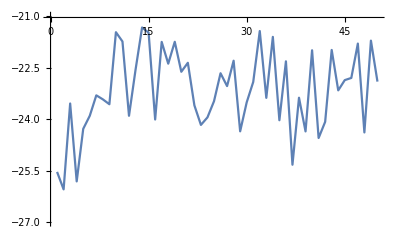

-23.173

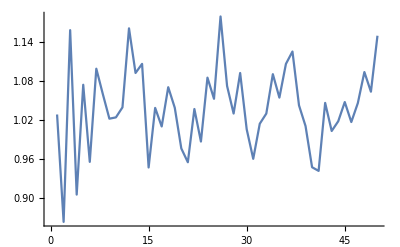

1.03921

```mathematica
data=Import["he4noip.vmc.1000.dat"];
En=Transpose[data][[4]];
errEn=Transpose[data][[6]];
ListPlot[En,Joined->True,PlotRange->{miny,maxy}]
Mean[En]
ListPlot[errEn,Joined->True]
Mean[errEn]
```

#### ip correlations 1000

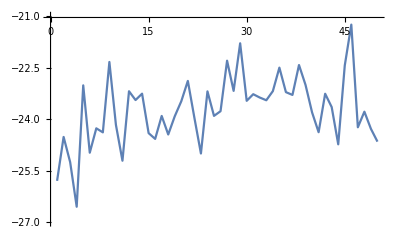

-23.7327

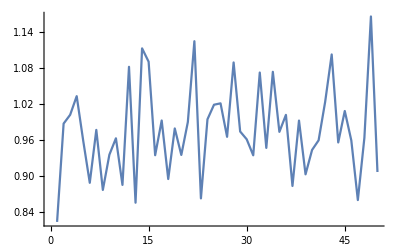

0.97651

```mathematica
data=Import["he4ip.vmc.1000.dat"];
En=Transpose[data][[4]];
errEn=Transpose[data][[6]];
ListPlot[En,Joined->True,PlotRange->{miny,maxy}]
Mean[En]
ListPlot[errEn,Joined->True]
Mean[errEn]
```

#### no ip correlations 24000

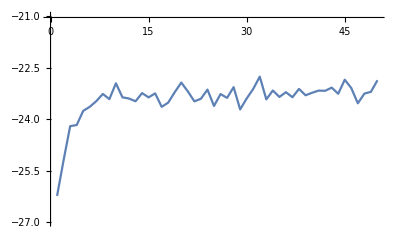

-23.4165

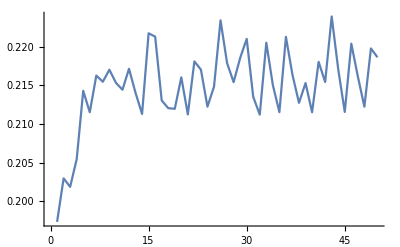

0.214832

```mathematica
data=Import["he4noip.vmc.24000.dat"];
En=Transpose[data][[4]];
errEn=Transpose[data][[6]];
ListPlot[En,Joined->True,PlotRange->{miny,maxy}]
Mean[En]
ListPlot[errEn,Joined->True]
Mean[errEn]
```

#### ip correlations 24000

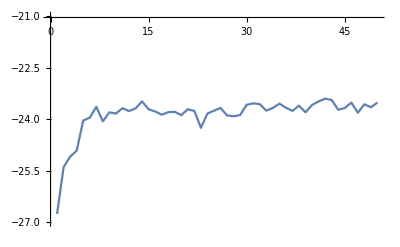

-23.8689

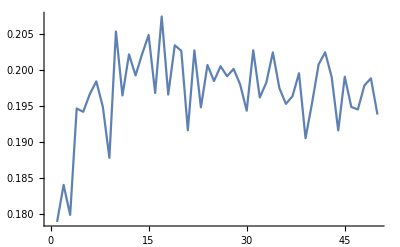

0.197112

```mathematica
data=Import["he4ip.vmc.24000.dat"];
En=Transpose[data][[4]];
errEn=Transpose[data][[6]];
ListPlot[En,Joined->True,PlotRange->{miny,maxy}]
Mean[En]
ListPlot[errEn,Joined->True]
Mean[errEn]
```

### Compare no corr and corr w=24000

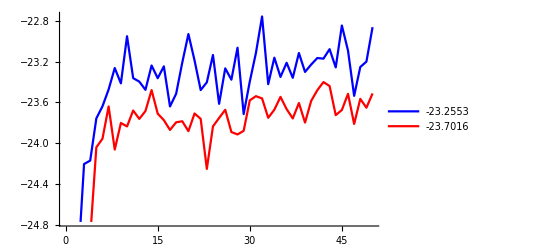

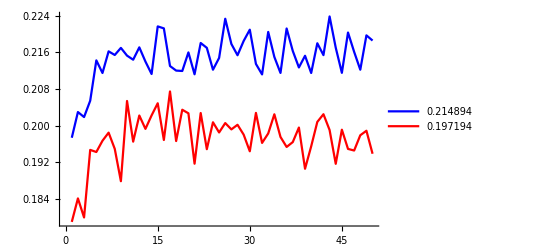

```mathematica
mmin=10;
corrdata=Import["he4ip.vmc.24000.dat"];
nocorrdata=Import["he4noip.vmc.24000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

No ip corelations: E=-23.3(2)
With ip correlations: E=-23.7(2)

#### no ip correlations dmc 10000

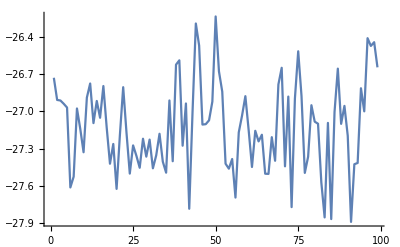

-27.1232

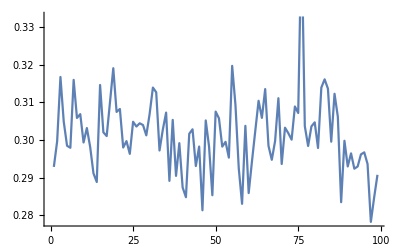

0.301451

```mathematica
data=Import["he4noip.dmc.10000.dat"];
En=Transpose[data][[4]];
En=En[[2;;Length[En]]];
errEn=Transpose[data][[6]];
errEn=errEn[[2;;Length[errEn]]];
ListPlot[En,Joined->True,PlotRange->All]
Mean[En]
ListPlot[errEn,Joined->True]
√(Total[errEn^2]/Length[errEn])
```

E0=-27.1(3) MeV

#### ip correlations dmc 10000

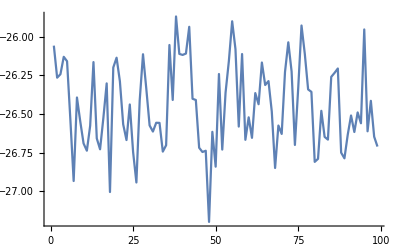

-26.4516

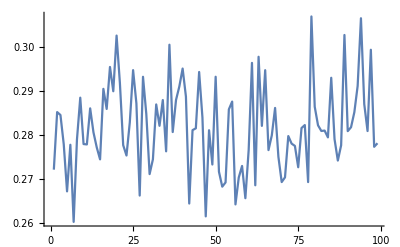

0.282042

```mathematica
data=Import["he4ip.dmc.10000.dat"];
En=Transpose[data][[4]];
En=En[[2;;Length[En]]];
errEn=Transpose[data][[6]];
errEn=errEn[[2;;Length[errEn]]];
ListPlot[En,Joined->True,PlotRange->All]
Mean[En]
ListPlot[errEn,Joined->True]
√(Total[errEn^2]/Length[errEn])
```

### Compare no corr and corr w=24000

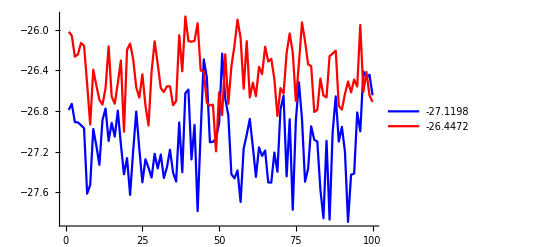

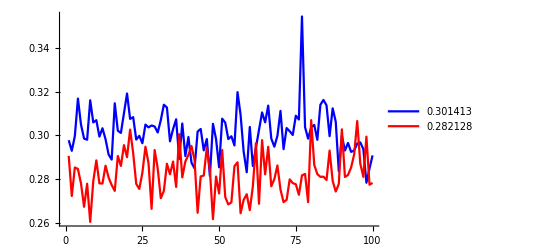

```mathematica
mmin=1;
corrdata=Import["he4ip.dmc.10000.dat"];
nocorrdata=Import["he4noip.dmc.10000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

No ip corelations: E=-27.1(3)
With ip correlations: E=-26.4(3)